# Model to describe the efficiency as a function of mass and ctau

```mathematica
f1[m_,E_,ct_,R_,z_]:=R/(2(E/m)ct(R^2+z^2))(Exp[(-√(R^2+z^2))/((E/m)ct)])  (* Exponencial decay of the GammaD *)
```

```mathematica
Zmax[m_,E_,ct_,R_]:= If[10.0 (E/m) ct<(10 R),10 (E/m) ct,10 R]
```

```mathematica
effR[R0_,R_]:= Which[R>0&&R<R0,1.0,R>R0,0.0] (* efficiency 1 before R0=9.8cm (3rd pixel layer) and zero above this value *)
```

```mathematica
Rmax[m_,E_,ct_]:=Which[10(E/m)ct<600,10(E/m)ct,10(E/m)ct≥600,600.0]
```

```mathematica
alpha0[m_]:=Which[m==0.25,0.0911856,m==0.4,0.0645557,m==0.7,0.0604557,m==1.0,0.0587443,m==5.0,0.0657431,m==8.5,0.127751] (*Efficiencies for ctau=0*)
```

```mathematica
datapoints= {{0.25,alpha0[0.25]},{0.4,0.06951},{0.7,alpha0[0.7]},{1.0,alpha0[1.0]},{5.0,alpha0[5.0]},{8.5,alpha0[8.5]}};
```

```mathematica
feffR=Interpolation[datapoints,InterpolationOrder->1];
```

```mathematica
f3[m_,E_,ct_]:=NIntegrate[effR[98.0,R]2f1[m,E,ct,R,z],{R,0.0,Rmax[m,E,ct]},{z,0.0,Zmax[m,E,ct,R]}]
```

```mathematica
alphavsctau[m_,E_,ct_]:=feffR[m] f3[m,E,ct] f3[m,E,ct]  (* Final expression of the model with to variables m and ctau, the Energy for the GamamD = 50 GeV which is mean value of distribution *)
```

### Calling external data for limit setting (Br, limit on N, f(m), etc...)

```mathematica
xsec = ReadList["/Users/Alfredo/Documents/GitHub/DarkPhoton_Limits_FTR/R_2016.dat",{Real,Real}];
```

```mathematica
R=Interpolation[xsec,InterpolationOrder->1]
```

InterpolatingFunction[{{0.36, 10.295}}, <>]

InterpolatingFunction::dmval: Input value {0.250169} lies outside the range of data in the interpolating function. Extrapolation will be used.

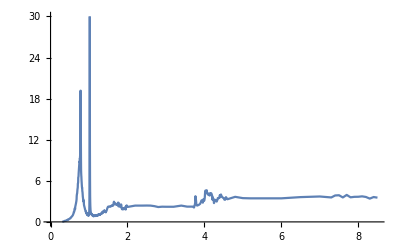

```mathematica
Plot[R[x],{x,0.25,8.5},PlotRange->{{0.0,8.5},{0.0,30.0}}]
```

```mathematica
a=0.18092712;b=0.36185895;c=0.08669159;d=1.30610993;e=3.08280157;f=0.04921893;g=6.80847652;h=2.03218775;i=0.99149336;
j=2.19107363
myGaus[x_,mu_,sigma_]:=1/(sigma*√(2 π))*Exp[-(x-mu)*(x-mu)/2.0/sigma/sigma]

Nlimitf[x_]:=a*myGaus[x,b,c]+d*myGaus[x,e,f]+g*myGaus[x,h,i]+j
```

2.19107

```mathematica
(* Model Independent Limit *)
```

```mathematica
(*Nlimitf[x_]:=2.4+0.196258*Exp[-0.5*((x-0.585342)/0.0400199)^2]+1.32241*Exp[-0.5*((x-0.833146)/0.0350001)^2]+0.893637*Exp[-0.5*((x-1.16449)/0.033)^2]+1.79953*Exp[-0.5*((x-1.41323)/0.03)^2]+0.59907*Exp[-0.5*((x-1.90641)/0.05)^2]+1.1*Exp[-0.5*((x-2.40133)/0.042)^2]+2.20401*Exp[-0.5*((x-2.999)/0.169458)^2]+3.57*Exp[-0.5*((x-3.1005)/0.134076)^2]
(*Fit parameters[0.18092712 0.36185895 0.08669159 1.30610993 3.08280157 0.04921893 6.80847652 2.03218775 0.99149336 2.19107363]
```

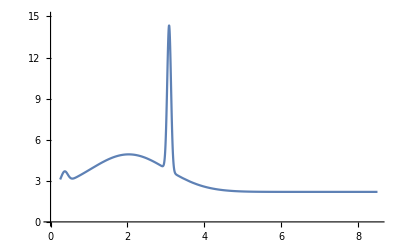

```mathematica
Plot[Nlimitf[x],{x,0.25,8.5},PlotRange->{{0.0,8.5},{0.0,15.0}}]
```

```mathematica
Br = ReadList["/Users/Alfredo/Documents/GitHub/DarkPhoton_Limits_FTR/Br_2016.dat",{Real,Real}]; (* Br  GammaD to 2 mu *)
```

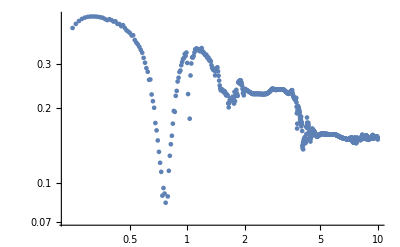

```mathematica
ListLogLogPlot[Br]
```

```mathematica
Brf = Interpolation[Br,InterpolationOrder->1]
```

InterpolatingFunction[{{0.25, 10.}}, <>]

```mathematica
listBrf = Table[{m,Brf[m]},{m,0.0,9.0,0.01}];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

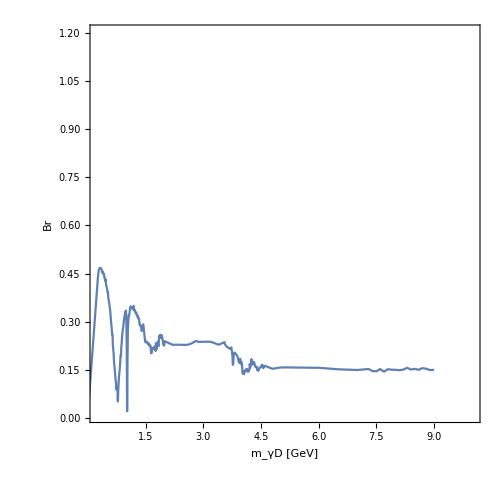

```mathematica
Brlog=ListPlot[listBrf,Joined->True,Joined->True,ImageSize->500,AspectRatio->1.0,TicksStyle->Directive[FontSize->16],Frame->True,FrameLabel->{"m_γD [GeV]","Br"},RotateLabel->True,BaseStyle->{FontSize->20},PlotRange->{{0.25,10.0},{0.01,1.2}}]
```

```mathematica
(* Partial witdths*)
```

```mathematica
alpha=0.0072973525664
```

0.00729735

```mathematica
masse= 0.000510998928
```

0.000510999

```mathematica
massmu= .1056583715
```

0.105658

```mathematica
ParWidthE[m_]:= 1/3 alpha m √(1-(4 masse^2)/m^2)(1+(2 masse^2)/m^2)
```

```mathematica
ParWidthM[m_]:= 1/3 alpha m √(1-(4 massmu^2)/m^2)(1+(2 massmu^2)/m^2)
```

```mathematica
ParWidthHad[m_]:= 1/3 alpha m √(1-(4 massmu^2)/m^2)(1+(2 massmu^2)/m^2)R[m]
```

```mathematica
ParWidthTot[m_]:= ParWidthE[m]+ParWidthM[m]+ParWidthHad[m]
```

```mathematica
1/ParWidthTot[1.0]
```

125.121

```mathematica
funfm[m_]:=1/ParWidthTot[m]
```

InterpolatingFunction::dmval: Input value {0.250179} lies outside the range of data in the interpolating function. Extrapolation will be used.

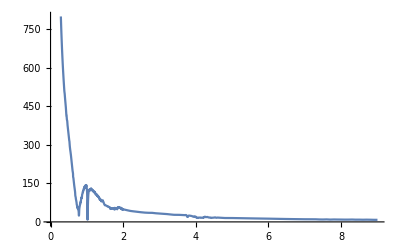

```mathematica
Plot[funfm[m],{m,0.25,9.0},PlotRange->{{0.0,9.0},{0.0,800}}]
```

#### Limit on Br(H→2γ) as a function of mass and ctau for different values (1%, 5%,10%,20%,40%)

```mathematica
(* Since we have epsilon as a function of the mass and ctau we cannot just plot the distributions as above, the limit is done in an iterative way getting the value in every mass bin and scanning in epsilon until it converges to the value of 3.07*)
```

```mathematica
ctauval[m_] := (1.97×10^-13 funfm[m])/10^Mineps2;  (* since our efficiency model is expresed in terms of ctau we need to correlate to which epsilon variable it correspond, at this step using epsilon^2 to avoid the sqrt *)
Nlimit2[m_,BrHtoGam_]:= 3000* 48580 * BrHtoGam *  alphavsctau[m,50,ctauval[m]]* Brf[m] * Brf[m];(* This is the expression for the limit this expresion will be evaluated in the mass and ctau space until it converges to a value close to the limit on N(m) *)
```

```mathematica
Labelepsvsctau={"cτ=100.0","cτ=50.0","cτ=20.0","cτ=10.0","cτ=5.0","cτ=3.0","cτ=1.0","cτ=0.1","cτ=0.001","cτ=0.00001"}
```

{cτ=100.0,cτ=50.0,cτ=20.0,cτ=10.0,cτ=5.0,cτ=3.0,cτ=1.0,cτ=0.1,cτ=0.001,cτ=0.00001}

```mathematica
Nlimit2[0.25,0.001]
```

InterpolatingFunction::dmval: Input value {0.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.212167

#### Br=0.1%

```mathematica
listbr01={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.001; (* value of Br(H->GammaD) *)
min= {0.25,2.5,3.5}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV for this Br=0.1% makes not much difference since the distribution doesnt go above mass aprox 0.7 GeV*)
mfin={2.5,3.5,9.0};
step={0.1,0.01,0.1};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.2; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-16.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.5 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-16.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn],Nlimitf[m]}];
AppendTo[listbr01,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,1,1}];
Export["/Users/Alfredo/Desktop/limite_DarkSUSY_FTR/Limit_epsvsmass_BrHtoGamD_01.dat",listbr01];
```

{{Null,Null}}

InterpolatingFunction::dmval: Input value {0.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{0.17,0.25,-10.96,3.5383,3.1082}

{0.17,0.35,-11.32,4.1027,3.67583}

{0.11,0.45,-11.56,3.52917,3.46454}

{0.16,0.55,-11.75,3.17903,3.17564}

{0.17,0.65,-11.86,3.41747,3.23939}

{0.16,0.75,-11.92,3.68069,3.38501}

{0.04,0.85,-12.05,3.89672,3.54153}

{0.15,0.95,-12.16,3.85923,3.70342}

{0.17,1.05,-12.22,4.31317,3.86787}

#### Br=1%

```mathematica
listbr1={{Null,Null}} (* This list will store the epsilon value in which the limit converges close to 3.07 *)
BrIn=0.01; (* value of Br(H->GammaD) *)
min= {0.25,0.7,0.85,1.0,1.2,2.0,3.5,5.0}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={0.7,0.85,1.0,1.2,2.0,3.5,5.0,9.0};
step={0.05,0.01,0.05,0.01,0.05,0.01,0.03,0.05};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.2; (* Initial steps to increase the 10^(epsilon^2)value*)
Mineps2=-16.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.5 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision demanded for the limit *)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-16.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0), (* once the limit value is above 3.07 break the loop *)
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01; (* If the limit was too far from the 3.07 repite the scan with finer steps *)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
AppendTo[listbr1,{m,Mineps2}]; (* Here the values will be stored for the whole mass range for specific Br *)
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,8,1}];
Export["/Users/Alfredo/Desktop/limite_DarkSUSY_FTR/Limit_epsvsmass_BrHtoGamD_1.dat",listbr1];
```

{{Null,Null}}

InterpolatingFunction::dmval: Input value {0.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

#### Br=5%

```mathematica
listbr5={{Null,Null}} (* To Store the limit value *)
BrIn=0.05; (* value of Br(H->GammaD) *)
min= {0.25,0.7,0.85,1.0,1.2,2.0,3.5,5.0}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={0.7,0.85,1.0,1.2,2.0,3.5,5.0,9.0};
step={0.05,0.01,0.05,0.01,0.1,0.1,0.1,0.1};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.2;
Mineps2=-16.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.5 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision or closenest to the 3.0*)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-16.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0),
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01;
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
AppendTo[listbr5,{m,Mineps2}];
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,8,1}];
Export["/Users/Alfredo/Desktop/limite_DarkSUSY_FTR/Limit_epsvsmass_BrHtoGamD_5.dat",listbr5];
```

{{Null,Null}}

InterpolatingFunction::dmval: Input value {0.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

#### Br=10%

```mathematica
listbr10={{Null,Null}} (* To Store the limit value *)
BrIn=0.1; (* value of Br(H->GammaD) *)
min= {0.25,0.7,0.85,1.0,1.2,2.0,3.5,5.0}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={0.7,0.85,1.0,1.2,2.0,3.5,5.0,9.0};
step={0.05,0.01,0.05,0.01,0.1,0.1,0.1,0.1};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.2;
Mineps2=-22.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.5 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision or closenest to the 3.0*)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-22.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0),
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01;
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
AppendTo[listbr10,{m,Mineps2}];
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,8,1}];
Export["/Users/Alfredo/Desktop/limite_DarkSUSY_FTR/Limit_epsvsmass_BrHtoGamD_10.dat",listbr10];
```

{{Null,Null}}

InterpolatingFunction::dmval: Input value {0.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

$Aborted

#### Br=20%

```mathematica
listbr20={{Null,Null}} (* To Store the limit value *)
BrIn=0.2; (* value of Br(H->GammaD) *)
min= {0.25,0.7,0.85,1.0,1.2,2.0,3.5,5.0}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={0.7,0.85,1.0,1.2,2.0,3.5,5.0,9.0};
step={0.05,0.01,0.05,0.01,0.05,0.05,0.01,0.05};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.2;
Mineps2=-16.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.5 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision or closenest to the 3.0*)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-16.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m] (*&& nval≠pval *)&& Mineps2<-4.0),
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01;
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
AppendTo[listbr20,{m,Mineps2}];
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,8,1}];
Export["/Users/Alfredo/Desktop/limite_DarkSUSY_FTR/Limit_epsvsmass_BrHtoGamD_20.dat",listbr20];
```

{{Null,Null}}

#### Br=40%

```mathematica
listbr40={{Null,Null}} (* To Store the limit value *)
BrIn=0.4; (* value of Br(H->GammaD) *)
min= {0.25,0.7,0.85,1.0,1.2,2.0,3.5,5.0}; (* Just to split the mass range different precision needed in dificult regions where the Br drops around 0.8 and 1.0 GeV*)
mfin={0.7,0.85,1.0,1.2,2.0,3.5,5.0,9.0};
step={0.05,0.01,0.05,0.01,0.1,0.1,0.1,0.1};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.2;
Mineps2=-16.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.5 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision or closenest to the 3.0*)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-16.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m](*&& nval≠pval *)&& Mineps2<-4.0),
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01;
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
AppendTo[listbr40,{m,Mineps2}];
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,8,1}];
Export["/Users/Alfredo/Desktop/limite_DarkSUSY_FTR/Limit_epsvsmass_BrHtoGamD_40.dat",listbr40];
```

{{Null,Null}}

InterpolatingFunction::dmval: Input value {0.25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

#### Br=60%

```mathematica
(listbr60={{Null,Null}} (* To Store the limit value *)
BrIn=0.6; (* value of Br(H->GammaD) *)
min= {0.25,0.7,0.8,1.0,1.1};
mfin={0.7,0.8,1.0,1.1,2.0};
step={0.05,0.001,0.05,0.01,0.1};
Table[
(*Print["  i  ",i,"   massmin  ",min[[i]],"   massf  ",mfin[[i]],"  step  ",step[[i]]];*)
Do[
(*pval=2.0;
nval=3.0;*)
iterbin=0.2;
Mineps2=-14.0;
(*Print[{"initial parameters","mass",m,"limit",Nlimit2[m,BrIn]}];*)
While[ (Abs[Nlimit2[m,BrIn]-Nlimitf[m]]>0.5 (*&& nval≠pval *)&& Mineps2<-4.0), (*0.5 is the precision or closenest to the 3.0*)
(*Print[{m,iterbin,Abs[Nlimit2[m,BrIn]-3.0]}];*)
Mineps2=-14.0;
While[
(Nlimit2[m,BrIn]<Nlimitf[m](*&& nval≠pval *)&& Mineps2<-4.0),
(*pval= Nlimit2[m,BrIn];*)
(*Print[{"oldval",pval}];*)
(*Print[{iterbin,Mineps2,Nlimit2[m,BrIn]}];*)
Mineps2 = Mineps2+iterbin;
(*nval= Nlimit2[m,BrIn];*)
(*Print[{m,Mineps2,Nlimit2[m,BrIn]}]*)
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
iterbin=iterbin-0.01;
];
(*Print[{iterbin,m,Mineps2,Nlimit2[m,BrIn]}];*)
AppendTo[listbr40,{m,Mineps2}];
,{m,min[[i]],mfin[[i]],step[[i]]}]
,{i,1,5,1}];
Export["/Users/Alfredo/Desktop/limite_DarkSUSY_FTR/Limit_epsvsmass_BrHtoGamD_60.dat",listbr60];
```

{{Null,Null}}

InterpolatingFunction::dmval: Input value {1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

### Plot the limit

```mathematica
(*Function to convert mass, Log[10,epsilon^{2}]   to   mass, epsilon*)
```

```mathematica
DataConvertermine[data_]:=Table[{data[[i,1]],√(10^data[[i,2]])},{i,Length[data]}]
```

```mathematica
Labelslin={"Br(H->2γ_D)=0.1%","Br(H->2γ_D)=1%","Br(H->2γ_D)=5%","Br(H->2γ_D)=10%","Br(H->2γ_D)=20%","Br(H->2γ_D)=40%"}
```

{Br(H->2γ_D)=0.1%,Br(H->2γ_D)=1%,Br(H->2γ_D)=5%,Br(H->2γ_D)=10%,Br(H->2γ_D)=20%,Br(H->2γ_D)=40%}

```mathematica
legendlin=SwatchLegend[{Darker[Cyan,0.2],Darker[Blue,0.2],Darker[Green,0.2],Darker[Yellow,0.2],Darker[Orange,0.2],Darker[Red,0.2],{Black,Dashed},{Purple,Dashed},{Brown,Dashed},{Cyan,Dashed},{Pink,Dashed}},Labelslin,LegendMarkerSize->{{15,15}},LabelStyle->{Italic,9},LegendMarkers->{"Line"}];
```

```mathematica
listbr01 = Import["/Users/Usuario/Desktop/limite_DarkSUSY_2017/Limit_epsvsmass_BrHtoGamD_01_2017.dat"];
listbr1   = Import["/Users/Usuario/Desktop/limite_DarkSUSY_2017/Limit_epsvsmass_BrHtoGamD_1_2017.dat"];
listbr5   = Import["/Users/Usuario/Desktop/limite_DarkSUSY_2017/Limit_epsvsmass_BrHtoGamD_5_2017.dat"];
listbr10 = Import["/Users/Usuario/Desktop/limite_DarkSUSY_2017/Limit_epsvsmass_BrHtoGamD_10_2017.dat"];
listbr20 = Import["/Users/Usuario/Desktop/limite_DarkSUSY_2017/Limit_epsvsmass_BrHtoGamD_20_2017.dat"];
listbr40 = Import["/Users/Usuario/Desktop/limite_DarkSUSY_2017/Limit_epsvsmass_BrHtoGamD_40_2017.dat"];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

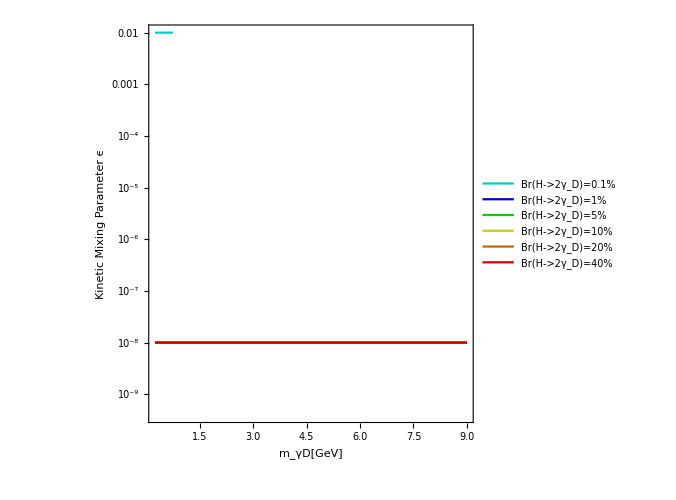

```mathematica
plotLimEpsilonvsmass = Legended[ListLogPlot[{DataConvertermine[DeleteCases[listbr01,{Null,Null}]],DataConvertermine[DeleteCases[listbr1,{Null,Null}]],DataConvertermine[DeleteCases[listbr5,{Null,Null}]],DataConvertermine[DeleteCases[listbr10,{Null,Null}]],DataConvertermine[DeleteCases[listbr20,{Null,Null}]],DataConvertermine[DeleteCases[listbr40,{Null,Null}]]}, Joined->True,PlotRange->{{0.25,9.0},{0.4 10^-9,0.1 10^-1}},ImageSize->500,AspectRatio->1.0,TicksStyle->Directive[FontSize->18],Frame->True,FrameLabel->{"m_γD[GeV]","Kinetic Mixing Parameter ϵ"},RotateLabel->True,BaseStyle->{FontSize->18},PlotStyle->{Darker[Cyan,0.2],Darker[Blue,0.2],Darker[Green,0.2],Darker[Yellow,0.2],Darker[Orange,0.2],Darker[Red,0.2],{Black,Dashed},{Purple,Dashed},{Brown,Dashed},{Cyan,Dashed},{Pink,Dashed}}],Placed[legendlin,{0.74,0.70}]]
```

```mathematica
Export["/Users/Usuario/Desktop/limite_DarkSUSY_2017/Limit_DarkPhoton_Epsilon_vs_mass_Run2.pdf",plotLimEpsilonvsmass]
```

/Users/Alfredo/Documents/Shared_Ubuntu/Limit_DarkPhoton_Epsilon_vs_mass_Run2.pdf